```mathematica
(* 
Generates figures for Carroll, Slacalek, Sommer: "Dissecting Saving Dynamics" 
*)
```

```mathematica
(* Initialization stuff; of no intrinsic interest *)
ClearAll["Global`*"];ParamsAreSet=False;
If[Length[$FrontEnd] > 0,NBDir=SetDirectory[NotebookDirectory[]]];(* If running from the Notebook interface *)
(* If running from shell, must start from inside same directory in which notebook resides *)
If[$VersionNumber<8,(*then*) Print["These programs require Mathematica version 8 or greater."];Abort[]];
(* Method of displaying figures depends on whether being run in batch mode or interactively *)
If[$FrontEnd == Null,OpenFigsUsingShell=True,OpenFigsUsingShell=False]; 
(* Current working directory should correspond to appropriate location now whether running from shell or notebook *)
AutoLoadDir=SetDirectory["../../CoreCode/Autoload"];Get["./init.m"];
(* CoreCode directory is above Autoload *)
CoreCodeDir=SetDirectory[".."];
(* root directory is above CoreCode *)
rootDir = SetDirectory[".."];
Get[CoreCodeDir<>"/MakeAnalyticalResults.m"];
Get[CoreCodeDir<>"/VarsAndFuncs.m"];
StableArmStyle={Black,Thick}; (* Allows for different style than in TractableBufferStock handout generated by the same code *)
TractableFigDir=SetDirectory[rootDir<>"/Examples/TractableBufferStock/Figures/"];
TractableCodeDir=SetDirectory[rootDir<>"/Examples/TractableBufferStock"];
cssUSSavingDirCode=SetDirectory[rootDir<>"/Examples/cssUSSaving"];cssUSSavingDirFigs=SetDirectory[rootDir<>"/Examples/cssUSSaving/Figures"];

VerboseOutput=False;
```

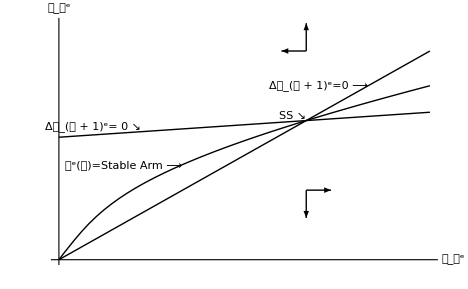

Exporting figure to /Volumes/Data/Code/Models/Tractable/Latest/EqbmPartial/Mathematica/Examples/cssUSSaving/Figures/TractableBufferStockPhaseDiag.xxx

```mathematica
(* Generate phase diagram *)

Get[CoreCodeDir<>"/ParametersBase.m"];
FindStableArm;
Get[TractableCodeDir<>"/cFunc.m"];
Get[TractableCodeDir<>"/PhaseDiag.m"];
ExportFigsToDir["TractableBufferStockPhaseDiag",cssUSSavingDirFigs];
```

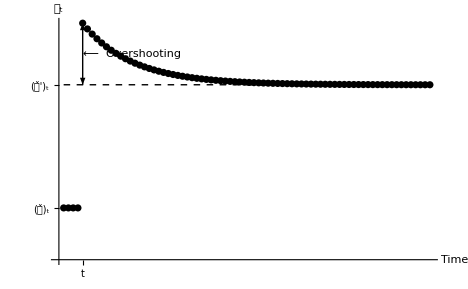

Exporting figure to /Volumes/Data/Code/Models/Tractable/Latest/EqbmPartial/Mathematica/Examples/cssUSSaving/Figures/savRateAfterMhoRisePlot.xxx

```mathematica
(* Show effects of increase in unemployment risk *)

Get[CoreCodeDir<>"/ParametersBase.m"];(* Restore the baseline parameter values *)
℧Base=℧=0.01;
ΓBase=Γ;
FindStableArm;
{κEBase,𝓂EBase,𝒸EBase} = {κE,𝓂E,𝒸E};
{𝓂Max,𝓂MaxMax}={1.5,5} 𝓂E;
𝒸LowerPlot=Plot[cE[𝓂],{𝓂,0,𝓂Max},PlotStyle->Dashing[{.01}]];
cEPFPlot = Plot[cEPF[𝓂],{𝓂,0,𝓂MaxMax},PlotStyle->Dashing[{.02}]];
Degree45 = Plot[𝓂,{𝓂,0,cE[𝓂MaxMax]},PlotStyle->Dashing[{.01}]];
cFuncPlotBase=cFuncPlot=Plot[cE[𝓂],{𝓂,0,𝓂MaxMax},PlotStyle->Black];
Stable𝓂LocusOrigPlot=Plot[{𝓂EDelEqZero[𝓂]},{𝓂,0,𝓂MaxMax},PlotStyle->Dashing[{.01}]];
(* Now increase unemployment risk by 2 percentage points *)
℧=℧Base+0.02;
FindStableArm;
cFuncPlotNew=Plot[cE[𝓂],{𝓂,0,𝓂MaxMax},PlotStyle->RGBColor[0,0,0]];
cFuncPlotNewPoints=Map[{{#,𝒸[#]}}&,Table[𝓂,{𝓂,0,𝓂MaxMax,0.01}]];
Stable𝓂LocusPlot=Plot[{𝓂EDelEqZero[𝓂]},{𝓂,0,𝓂MaxMax},PlotStyle->Dashing[{.01}]];
Stable𝓂LocusPoints=Map[{{#,𝓂EDelEqZero[#]}}&,Table[𝓂,{𝓂,0,𝓂MaxMax,0.1}]];

SimGeneratePath[𝓂EBase,100];
𝓂𝒸PathPlot = ListPlot[𝓂𝒸Path,PlotStyle->{PointSize[0.015]}];
{𝓂MinNew,𝓂MaxNew}={0,5};
{𝒸MinNew,𝒸MaxNew}={0,1.5};
TractableBufferStockTarget = Show[cFuncPlotBase,Stable𝓂LocusPlot,Stable𝓂LocusOrigPlot
,Graphics[Text["Target ⟶",{𝓂EBase,1.02𝒸EBase},{1,0}]]
,Graphics[Text[" ⟵ Sustainable 𝒸",{𝓂E,0.98𝒸E},{-1,0}]]
,Graphics[Text["c(𝓂) ⟶",{0.7𝓂EBase,0.85𝒸EBase},{1,0}]]
,Ticks->None
       ,PlotRange->{{𝓂MinNew,𝓂MaxNew},{𝒸MinNew,𝒸MaxNew}}
       ,AxesLabel->{"𝓂","𝒸"}];
OldAndNewcFuncsPlot = Show[Stable𝓂LocusPlot,cFuncPlotBase,cFuncPlotNew
,PlotRange->{{0,𝓂MaxMax},{0,Automatic}}
,AxesOrigin->{0.,0.}
];

PhaseDiagramIncreaseMhoPlot = Show[OldAndNewcFuncsPlot,𝓂𝒸PathPlot,Stable𝓂LocusOrigPlot
,Graphics[Text["Orig Target ⟶",{𝓂EBase,1.02𝒸EBase},{1,0}]]
,Graphics[Text["New Target↘",{𝓂E,1.04𝒸E},{1,0}]]
,Graphics[Text["Orig c(𝓂) ⟶",{1.25𝓂EBase,1.2𝒸EBase},{1,0}]]
,Graphics[Text[" ⟵ New c(𝓂)",{𝓂EBase,cE[𝓂EBase]},{-1,0}]]
,Ticks->None
,AxesLabel->{"𝓂","𝒸"}
,PlotRange->{{𝓂MinNew-1,𝓂E+2},{𝒸MinNew,1.3𝒸EBase}}
,AxesOrigin->{0.,0.}
];

HowMany=75;
𝓂Path=Take[Transpose[𝓂𝒸Path][[1]],HowMany];
𝒸Path=Take[Transpose[𝓂𝒸Path][[2]],HowMany];
(*savRateBase = (𝓂EBase-1)/(R/);*)
MPCPath=Map[cE'[#]&,Rest[𝓂Path]];
PrependTo[𝓂Path,𝓂EBase];
PrependTo[𝒸Path,𝒸EBase];
PrependTo[𝓂Path,𝓂EBase];
PrependTo[𝒸Path,𝒸EBase];
PrependTo[𝓂Path,𝓂EBase];
PrependTo[𝒸Path,𝒸EBase];
PrependTo[MPCPath,κEBase];
PrependTo[MPCPath,κEBase];
PrependTo[MPCPath,κEBase];
PrependTo[MPCPath,κEBase];
timePath=Table[i,{i,Length[𝒸Path]}];
𝒸PathPlot = ListPlot[Transpose[{timePath,𝒸Path}],PlotRange->All];
𝓂PathPlot = ListPlot[Transpose[{timePath,𝓂Path}],PlotRange->All];
MPCPathPlot = ListPlot[Transpose[{timePath,MPCPath}],PlotRange->All];

cPathAfterMhoRise=Show[𝒸PathPlot
,Ticks->{{{4,"0"}},None}
,AxesLabel->{"Time","𝒸_𝓉^e"}
,AxesOrigin->{-3,0}
,PlotRange->{{-3,Automatic},{0,Automatic}}
];
(*
ExportFigsToDir["cPathAfterMhoRise",cssUSSavingDirFigs];
Show[cPathAfterMhoRise]
*)

mPathAfterMhoRise=Show[𝓂PathPlot
,Ticks->{{{4,"0"}},None}
,AxesLabel->{"Time","𝓂_𝓉^e"}
,PlotRange->{{-3,HowMany},{0,Automatic}}
,AxesOrigin->{-3,0}
,PlotRange->{{-3,Automatic},{0,Automatic}}
];
(*
ExportFigsToDir["mPathAfterMhoRise",cssUSSavingDirFigs];
Show[mPathAfterMhoRise]
*)

MPCPathAfterMhoRise=Show[MPCPathPlot
,Graphics[{Dashing[{0.01}],Line[{{timePath[[1]],κ},{timePath[[-1]],κ}}]}]
,Graphics[Text["↑",{(timePath[[1]]+timePath[[-1]])/2,κ},{0,1}]]
,Graphics[Text["Perfect Foresight MPC",{(timePath[[1]]+timePath[[-1]])/2,κ(4/5)},{0,1}]]
,Ticks->{{{4,"0"}},None}
,AxesLabel->{"Time","κ_𝓉"}
,PlotRange->All
,AxesOrigin->{-3,0.}];

(*
ExportFigsToDir["MPCPathAfterMhoRise",cssUSSavingDirFigs];
Show[MPCPathAfterMhoRise]
*)

(*
ExportFigsToDir["PhaseDiagramIncreaseMhoPlot",cssUSSavingDirFigs];
Show[PhaseDiagramIncreaseMhoPlot]
*)

savRatePath=((𝓂Path-1)(R-1)+1-𝒸Path)/((𝓂Path-1)(R-1)+1);
savRateAfterMhoRiseRaw=ListPlot[savRatePath,PlotRange->All];
savRateAfterMhoRisePlot=Show[savRateAfterMhoRiseRaw
,Graphics[{Dashing[0.01],Line[{{1,savRatePath[[-1]]},{Length[savRatePath],savRatePath[[-1]]}}]}]
,Graphics[{Arrowheads[{-.025,.025}],Arrow[{{5,savRatePath[[-1]]},{5,savRatePath[[5]]}}]}]
,Graphics[Text[" ⟵  Overshooting",{5,(savRatePath[[-1]]+savRatePath[[5]])/2},{-1,0}]]
,Ticks->{{{5,"t"}},{{savRatePath[[1]],"(𝓈̌)_t"},{savRatePath[[-1]],"(𝓈̌')_t"}}}
,AxesLabel->{"Time","𝓈_t"}
,BaseStyle->{FontSize->18}
];
ExportFigsToDir["savRateAfterMhoRisePlot",cssUSSavingDirFigs];
```

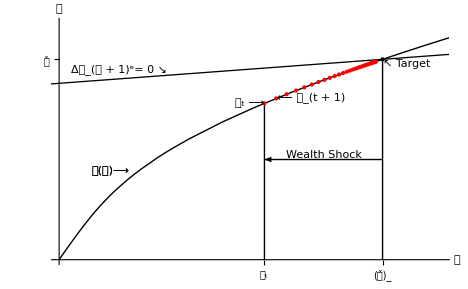

Exporting figure to /Volumes/Data/Code/Models/Tractable/Latest/EqbmPartial/Mathematica/Examples/cssUSSaving/Figures/WealthShock.xxx

```mathematica
(* Wealth shock *)

Get[CoreCodeDir<>"/ParametersBase.m"];
𝓂Max=1.5 𝓂E;
𝓂MaxMax=5 𝓂E;
FindStableArm;
cFuncPlotBase=cFuncPlot=Plot[cE[𝓂],{𝓂,0,𝓂MaxMax}];
Stable𝓂LocusPlot=Plot[{𝓂EDelEqZero[𝓂]},{𝓂,-0.2,𝓂MaxMax},PlotStyle->{Black,Thickness[0.002]}];
WealthShockSize=2;
SimGeneratePath[𝓂E-WealthShockSize,30];
{𝓂MinNew,𝓂MaxNew}={0,20};
{𝒸MinNew,𝒸MaxNew}={0,2.};
𝓂𝒸PathPlot = ListPlot[Take[𝓂𝒸Path,-(Length[𝓂𝒸Path]-1)],PlotStyle->{Red,PointSize[Medium]}];WealthShock=Show[cFuncPlotBase,Stable𝓂LocusPlot,𝓂𝒸PathPlot
,Graphics[Text["\!\(\*SubsuperscriptBox[\(Δ𝓂\), \(𝓉 + 1\), \(e\)]\)= 0 ↘",{𝓂E/3,𝓂EDelEqZero[𝓂E/3]},{1,-1}]]
,Graphics[Text["𝒸(𝓂)⟶",{0.1 𝓂E,0.45 𝒸E},{-1,0}]]
,Graphics[Line[{{𝓂E,0},{𝓂E,𝒸E}}]]
,Graphics[Line[{{𝓂E-2,0},{𝓂E-2,cE[𝓂E-2]}}]]
,Graphics[Arrow[{{𝓂E,𝒸E/2},{𝓂E-2,𝒸E/2}}]]
,Graphics[Text["𝒸_t ⟶",{𝓂E-2,cE[𝓂E-2]},{1,0}]]
,Graphics[Text[" ⟵ 𝒸_(t + 1)",{𝓂E-2+0.22,cE[𝓂E-2+0.22]},{-1,0}]]
,Graphics[Text["Wealth Shock",{𝓂E-1,𝒸E/2},{0,-1}]]
,Graphics[Text[" ↖ Target",{𝓂E,𝒸E},{-1,1}]]
,Graphics[Text["𝒸(𝓂)⟶",{0.1 𝓂E,0.45 𝒸E},{-1,0}]]
,Graphics[{Black,PointSize[Medium],Point[{𝓂E,𝒸E}]}]
,Ticks->{{{𝓂E,"(𝓂̌)_"},{𝓂E-2,"𝓂_t"}},{{𝒸E,"𝒸̌"}}}
,PlotRange->{{𝓂MinNew,𝓂E+1},{𝒸MinNew,𝒸E+.2}}
,AxesLabel->{"𝓂","𝒸"}];
ExportFigsToDir["WealthShock",cssUSSavingDirFigs];
```

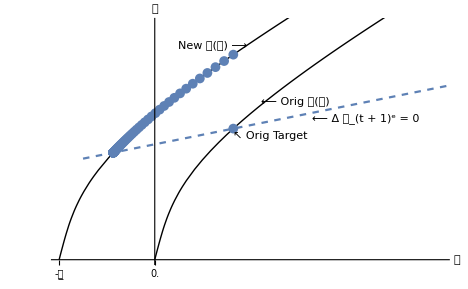

Exporting figure to /Volumes/Data/Code/Models/Tractable/Latest/EqbmPartial/Mathematica/Examples/cssUSSaving/Figures/PhaseDiagramDebtLimRisePlot.xxx

```mathematica
(* Increase in natural borrowing limit *)

Get[CoreCodeDir<>"/ParametersBase.m"];𝔤   =𝔤Base   =0.01;
{𝒸EBase,𝓂EBase,κEBase} = a{𝒸E,𝓂E,κE};
𝓂Max=1.5 𝓂E;
𝓂MaxMax=5 𝓂E;
FindStableArm;
κEBase = κE //N;𝒸EBase = 𝒸E //N;𝓂EOrig=𝓂EBase //N;
DebtLimPDV=0.2/((R)-𝔊);Stable𝓂LocusPlot=Plot[{𝓂EDelEqZero[𝓂]},{𝓂,-DebtLimPDV,𝓂MaxMax},PlotStyle->{Black,Thickness[0.002]}];
StableArmStyle={Black,Thick}; (* Allows for different style than in TractableBufferStock handout *)
{𝓂MinNew,𝓂MaxNew}={0,20};
{𝒸MinNew,𝒸MaxNew}={0,2.};
𝒸LowerPlot=Plot[cE[𝓂],{𝓂,0,𝓂Max},PlotStyle->Dashing[{.01}]];
cEPFPlot = Plot[cEPF[𝓂],{𝓂,0,𝓂MaxMax},PlotStyle->Dashing[{.02}]];
Degree45 = Plot[𝓂,{𝓂,0,cE[𝓂MaxMax]},PlotStyle->Dashing[{.01}]];
cFuncPlotBase=cFuncPlot=Plot[cE[𝓂],{𝓂,0,𝓂MaxMax},PlotStyle->Black];
cFunc=Show[cFuncPlotBase,Stable𝓂LocusPlot
,Graphics[Text["↖ Sustainable 𝒸",{0.6 𝓂E,0.9 𝒸E},{1,0}]],Graphics[Text["𝒸(𝓂)⟶",{0.1 𝓂E,0.45 𝒸E},{-1,0}]]
,Graphics[{Thickness[0.002],Dashing[{0.02}],Line[{{𝓂E,0},{𝓂E,𝒸E}}]}]
,Graphics[{Thickness[0.002],Dashing[{0.02}],Line[{{0,𝒸E},{𝓂E,𝒸E}}]}]
,Graphics[Text[" ↖ Target",{𝓂E,𝒸E},{-1,1}]]
,Graphics[Text["𝒸(𝓂)⟶",{0.1 𝓂E,0.45 𝒸E},{-1,0}]]
,Graphics[{Black,PointSize[Medium],Point[{𝓂E,𝒸E}]}]
,Ticks->{{{𝓂E,"(𝓂̌)_"}},{{𝒸E,"𝒸̌"}}}
,PlotRange->{{𝓂MinNew,𝓂E+1},{𝒸MinNew,𝒸E+.2}}
,AxesLabel->{"𝓂","𝒸"}];
Get[CoreCodeDir<>"/ParametersBase.m"];
(* Restore the baseline parameter values and solve again *)
{ r ,ϑ ,𝔤,℧}={rBase,ϑBase,𝔤Base,℧Base};
𝓂Max=1.5 𝓂E;
𝓂MaxMax=5 𝓂E;
FindStableArm;
κEBase = κE //N;𝒸EBase = 𝒸E //N;
cFuncPlotBasePoints=Map[{{#,cE[#]}}&,Table[𝓂,{𝓂,0,𝓂MaxMax,0.01}]];
cFuncPlotBase=cFuncPlot=Plot[cE[𝓂],{𝓂,0,𝓂MaxMax},PlotStyle->StableArmStyle];
Stable𝓂LocusPlot=Plot[{𝓂EDelEqZero[𝓂]},{𝓂,-5,𝓂MaxMax},PlotStyle->Dashing[{0.01}]];
(* Now suppose that there is an exogenous perfectly certain increase to permanent income by the amount 0.2 per year - think of it as a government transfer received by everyone in the population (this is equivalent to but more transparent than introducing unemployment insurance) *)
DebtLimPDV=0.2/((R)-𝔊);
cEwithNewDebtLim[m_]:= cEInterp[m+DebtLimPDV];
SimGeneratePathUsing[cEwithNewDebtLim,𝓂E,100]; 
cFuncPlotNew=Plot[cEwithNewDebtLim[𝓂],{𝓂,-DebtLimPDV,𝓂MaxMax},PlotRange->All,PlotStyle->StableArmStyle];
𝓂𝒸PathPlot = ListPlot[𝓂𝒸Path,PlotStyle->{PointSize[0.015]}];
{𝓂MinNew,𝓂MaxNew}={0,20};
{𝒸MinNew,𝒸MaxNew}={0,2.};TractableBufferStockTarget=Show[cFuncPlotBase,Stable𝓂LocusPlot,Graphics[Text["Perm Inc ⟶",{0.6 𝓂E,0.98 𝒸E},{1,0}]],Graphics[Text["⟵ 𝒸(𝓂)",{0.9 𝓂E,0.85 𝒸E},{-1,0}]],Ticks->None
,PlotRange->{{𝓂MinNew,𝓂E+1},{𝒸MinNew,𝒸E+rBase}}
,AxesLabel->{"𝓂","𝒸"}];

PhaseDiagramDebtLimRisePlot=Show[cFuncPlotNew,cFuncPlotBase,𝓂𝒸PathPlot,Stable𝓂LocusPlot
,Graphics[Text["↖ Orig Target ",{𝓂EBase,0.98 𝒸EBase},{-1,1}]]
,Graphics[Text["⟵ Δ 𝓂_(t + 1)^e = 0",{2𝓂EBase,𝓂EDelEqZero[2𝓂EBase]},{-1,1}]]
,Graphics[Text[" ⟵ Orig 𝒸(𝓂) ",{1.35 𝓂EBase,1.2 𝒸EBase},{-1,0}]]
,Graphics[Text["  New 𝒸(𝓂) ⟶ ",{𝓂EBase+1,cEwithNewDebtLim[𝓂EBase+1]},{1,0}]]
,PlotRange->{{-DebtLimPDV,𝓂MaxNew},{𝒸MinNew,𝒸MaxNew}}
,AxesLabel->{"𝓂","𝒸"}
,Ticks->{{{-DebtLimPDV,"-𝒽̲"},{0,"0."}},None}];
ExportFigsToDir["PhaseDiagramDebtLimRisePlot",cssUSSavingDirFigs];
```